## 2MBA50 Mathematica Practicum 3 exercises

This series of notebooks is made in Mathematica 13.3

Contact: Jan Willem Knopper, MF 5.121, j.w.knopper@tue.nl
Author: ir. W.J.P.M. Kortsmit, small adjustments by Benne de Weger, and Jan Willem Knopper.

## Section. More examples and applications.

### Name:

### Exercises

#### Exercise Section.Equation

Draw the graphs of the functions f_n(x)=√(n/π) ⅇ^(-n x^2) for n =1,2,3,..,8 for x on the interval [-2,2] in one figure.

#### Answer

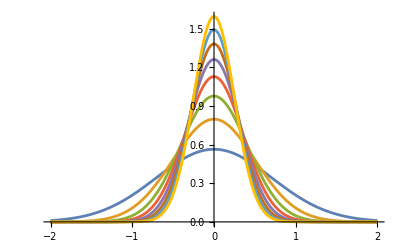

```mathematica
Plot[Evaluate[Table[Sqrt[n/Pi]*E^(-n*x^2),{n,1,8}]],{x,-2,2}]
```

#### Exercise Section.Equation

Look up the following concepts with the help function: ListPlot and PointSize.
a) Make a table of the pairs (x,y) , where x goes from -3 up to and including 3 with steps of 0.5 and y=100 sin(x). 
b) Draw these points in the plane. 
c) Now use the help function for the option: Joined. Then make a curve through these points.

#### Answer

```mathematica
"a)"
Table[{x,100*Sin[x]},{x,-3,3,0.5}]
"b)"
ListPlot[%]
"c)"
ListPlot[%%, Joined -> True]
```

a)

{{-3.,-14.112},{-2.5,-59.8472},{-2.,-90.9297},{-1.5,-99.7495},{-1.,-84.1471},{-0.5,-47.9426},{0.,0.},{0.5,47.9426},{1.,84.1471},{1.5,99.7495},{2.,90.9297},{2.5,59.8472},{3.,14.112}}

b)

ListPlot::lpn: b) is not a list of numbers or pairs of numbers.

ListPlot[b)]

c)

ListPlot::lpn: False is not a list of numbers or pairs of numbers.

ListPlot::lpn: b) is not a list of numbers or pairs of numbers.

ListPlot::lpn: ListPlot[b)] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[ListPlot[b)],Joined→True]

#### Exercise Section.Equation

Use the help function to look up the following concepts: Re, Im and ComplexExpand. Also look up the newer functions ReIm and ComplexListPlot.
a) Solve the equation: z^4 = 8 √3  + 8ⅈ and 
b) draw the solutions in the complex plane by using Mathematica. 
Hint: Often a solution is returned as replacement rules. To get a list it is often possible to use something like  z/. rules

#### Answer

```mathematica
"a)"
Solve[z^4 == 8*Sqrt[2] + 8*I]
"b)"
ComplexListPlot[z/.%]
```

a)

{{z→-2^(3/4) (ⅈ+√2)^(1/4)},{z→-ⅈ 2^(3/4) (ⅈ+√2)^(1/4)},{z→ⅈ 2^(3/4) (ⅈ+√2)^(1/4)},{z→2^(3/4) (ⅈ+√2)^(1/4)}}

b)

ReplaceAll::reps: {b)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ComplexListPlot::ldata: z/.b) is not a valid dataset or list of datasets.

ComplexListPlot[z/.b)]

#### Exercise Section.Equation

Look up with the help function: PolynomialRemainder and PolynomialQuotient. 
Compute the remainder and quotient polynomial of  (p(x))/(q(x)) for the cases a) b) and c) below. 
Think how you would do this calculation by hand and try to predict the degree of the result would have and then calculate it using Mathematica.
a. p(x)=ⅈ x^3-3 x+2 ⅈ+1, q(x)=3 x-2.
b. p(x)=x^8-x^6+1, q(x)=x^2+1.
c. p(x)=x^5+(ⅈ+3) x^2+1, q(x)=x^3+ⅈ.
d. For which values of a does the polynomial p(x)=x^4+(a^2-a-2) x^3+(a^3-2 a^2-2 a+3) x^2+(2 a^2-3 a-4) x+2 contain a factor x^2+x+1?

#### Answer

```mathematica
"a)"
p := I * x^3-3x+2I+1
q := 3x-2
PolynomialRemainder[p,q,x]
PolynomialQuotient[p,q,x]

"b)"
p := x^8-x^6+1
q := x^2+1
PolynomialRemainder[p,q,x]
PolynomialQuotient[p,q,x]

"c)"
p := x^5+(I+3)*x^2+1
q := x^3+I
PolynomialRemainder[p,q,x]
PolynomialQuotient[p,q,x]

"d)"
p:=x^4+(a^2-a-2) *x^3+(a^3-2 *a^2-2* a+3) *x^2+(2 *a^2-3* a-4)* x+2
q:=x^2+x+1
Solve[PolynomialRemainder[p,q,x]==0,a]
```

a)

-1+(62 ⅈ)/27

(-1+(4 ⅈ)/27)+(2 ⅈ x)/9+(ⅈ x^2)/3

b)

3

-2+2 x^2-2 x^4+x^6

c)

1+3 x^2

x^2

d)

{{a→-1},{a→3},{a→(1+2 x)/(1+x)}}

#### Exercise Section.Equation

a. Consider the expression (7 x+3)/(x-1)+x/(x^3-1)+x+5. Bring the terms under a common denominator and expand. Now determine an antiderivative and differentiate the result. Show that the now obtained answer is equal to the original expression.

b. Differentiate the expression (3 x^4-7 x^3-3 x^2+4 x-4)/(x^3-3 x^2+x-1) twice and bring the result under a common denominator. Now integrate twice to x and determine the difference between this result and the original expression. Explain the answer.

#### Answer

```mathematica
"a)"
Together[(7 x+3)/(x-1)+x/(x^3-1)+x+5]
Expand[%]
Integrate[%,x]
D[%,x]
Equal[Simplify[%],Simplify[%%%%]]

"b)"
ex :=(3 x^4-7 x^3-3 x^2+4 x-4)/(x^3-3 x^2+x-1)
D[ex,{x,2}]
Together[%]
Integrate[Integrate[%, x],x]
Simplify[ex - %]
Explanation:="Since we integrate twice there are two successive constants of integration where differences may occure. This gives us a difference of ax+b for some a and some b."
```

a)

(-2+10 x+10 x^2+12 x^3+x^4)/((-1+x) (1+x+x^2))

-2/((-1+x) (1+x+x^2))+(10 x)/((-1+x) (1+x+x^2))+(10 x^2)/((-1+x) (1+x+x^2))+(12 x^3)/((-1+x) (1+x+x^2))+x^4/((-1+x) (1+x+x^2))

12 x+x^2/2+ArcTan[(1+2 x)/(√3)]/(√3)+7 Log[1-x]-7/2 Log[1+x+x^2]+10/3 Log[1-x^3]

12-7/(1-x)+x-(7 (1+2 x))/(2 (1+x+x^2))-(10 x^2)/(1-x^3)+2/(3 (1+1/3 (1+2 x)^2))

True

b)

(-6-42 x+36 x^2)/(-1+x-3 x^2+x^3)-(2 (1-6 x+3 x^2) (4-6 x-21 x^2+12 x^3))/((-1+x-3 x^2+x^3)^2)+(-4+4 x-3 x^2-7 x^3+3 x^4) ((2 (1-6 x+3 x^2)^2)/((-1+x-3 x^2+x^3)^3)-(-6+6 x)/((-1+x-3 x^2+x^3)^2))

(2 (9-33 x-30 x^2+88 x^3-57 x^4+15 x^5))/((-1+x-3 x^2+x^3)^3)

(-2+5 x)/(-1+x-3 x^2+x^3)

2+3 x

#### Exercise Section.Equation

Determine the following integrals and verify the result by differentiating again:
a. ∫x^3 sin(x^2)ⅆx
b. ∫log^10(x)ⅆx
c. ∫1/((1-x^2)^2)ⅆx
d. ∫1/(x^4+1)ⅆx

#### Answer

```mathematica
"a)"
Integrate[x^3 Sin[x^2],x]
D[%,x]
"b)"
Integrate[Log[x]^10,x]
D[%,x]
"c)"
Integrate[1/((1-x^2)^2),x]
Simplify[D[%,x]]
"d)"
Integrate[1/(x^4+1),x]
Simplify[D[%,x]]
```

a)

-1/2 x^2 Cos[x^2]+Sin[x^2]/2

x^3 Sin[x^2]

b)

3628800 x-3628800 x Log[x]+1814400 x Log[x]^2-604800 x Log[x]^3+151200 x Log[x]^4-30240 x Log[x]^5+5040 x Log[x]^6-720 x Log[x]^7+90 x Log[x]^8-10 x Log[x]^9+x Log[x]^10

Log[x]^10

c)

1/4 (-(2 x)/(-1+x^2)-Log[1-x]+Log[1+x])

1/((-1+x^2)^2)

d)

(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4 √2)

1/(1+x^4)

#### Exercise Section.Equation

a) Compute (1)∫_-π^π cos(a x) cos(b x)ⅆx (1) , (2) ∫_-π^π sin(a x) sin(b x)ⅆx and (3) ∫_-π^π sin(a x) cos(b x)ⅆx. Here a and b are real numbers. 
b) What are the results if a and b are integers? 
c) What are the results if a and b are the same integer?

d) Compute (1) ∫ⅇ^(-a x) sin(b x)ⅆx and (2) ∫ⅇ^(-a x) cos(b x)ⅆx. Here a and b are real numbers with a>0. 
e) What are the results if we let x go from 0 to ∞?
f) Also compute ∫_0^∞ ⅇ^-x |sin(x)|ⅆx.

#### Answer

```mathematica
"a)"
Integrate[Cos[a*x]*Cos[b*x],{x,-Pi,Pi}]
Integrate[Sin[a*x]*Sin[b*x],{x,-Pi,Pi}]
Integrate[Sin[a*x]*Cos[b*x], {x,-Pi,Pi}]
"b)"
Assuming[Element[a,Integers] && Element[b,Integers], Integrate[Cos[a*x]*Cos[b*x],{x,-Pi,Pi}]]
Assuming[Element[a,Integers] && Element[b,Integers], Integrate[Sin[a*x]*Sin[b*x],{x,-Pi,Pi}]]
Assuming[Element[a,Integers] && Element[b,Integers], Integrate[Sin[a*x]*Cos[b*x], {x,-Pi,Pi}]]

"c)"
Assuming[Element[a,Integers] && Element[b,Integers] && a==b, Integrate[Cos[a*x]*Cos[b*x],{x,-Pi,Pi}]]
Assuming[Element[a,Integers] && Element[b,Integers] && a==b, Integrate[Sin[a*x]*Sin[b*x],{x,-Pi,Pi}]]
Assuming[Element[a,Integers] && Element[b,Integers] && a==b, Integrate[Sin[a*x]*Cos[b*x], {x,-Pi,Pi}]]

"d)"
Assuming[a>0 , Integrate[E^(-a*x) Sin[b*x],x]]
Assuming[a>0  , Integrate[E^(-a*x) Cos[b*x],x]]

"e)"
Assuming[a>0&& Element[b, Reals], Integrate[E^(-a*x) Sin[b*x],{x,0,Infinity}]]
Assuming[a>0&& Element[b, Reals], Integrate[E^(-a*x) Cos[b*x],{x,0, Infinity}]]

"f)"
Simplify[Integrate[E^(-x)*Abs[Sin[x]], {x,0,Infinity}]]
```

a)

(2 a Cos[b π] Sin[a π]-2 b Cos[a π] Sin[b π])/(a^2-b^2)

(2 b Cos[b π] Sin[a π]-2 a Cos[a π] Sin[b π])/(a^2-b^2)

0

b)

0

0

0

c)

π

π

0

d)

-(ⅇ^(-a x) (b Cos[b x]+a Sin[b x]))/(a^2+b^2)

(ⅇ^(-a x) (-a Cos[b x]+b Sin[b x]))/(a^2+b^2)

e)

b/(a^2+b^2)

a/(a^2+b^2)

f)

(1+ⅇ^π)/(-2+2 ⅇ^π)

#### Exercise Section.Equation

Use the help function to look up the functions TrigReduce, TrigFactor and TrigExpand. 
a) Reduce the following expressions in which sin(ax) and cos(ax) can occur for different a, but each sin and cos at most up to the first power. First think of which formulas you would use when doing these calculations by hand (but you don’t need to write them in the answer) and then calculate the result with Mathematica.
1. sin(4 x) cos(2 x) cos^2(3 x)
2. cos^7(x)
3. cos^4(2x)-sin^2(2x)
b) Also reduce these expressions to expressions in which only sin(x) and cos(x) occur, but in which all powers of sin(x) and cos(x) are allowed.

#### Answer

```mathematica
"a)"
TrigReduce[Sin[4x]Cos[2x]Cos[3x]^2]
TrigReduce[Cos[x]^7]
TrigReduce[Cos[2x]^4-Sin[2x]^2]

"b)"
TrigExpand[Sin[4x]Cos[2x]Cos[3x]^2]
TrigExpand[Cos[x]^7]
TrigExpand[Cos[2x]^4-Sin[2x]^2]
```

a)

1/8 (2 Sin[2 x]-Sin[4 x]+2 Sin[6 x]+Sin[8 x]+Sin[12 x])

1/64 (35 Cos[x]+21 Cos[3 x]+7 Cos[5 x]+Cos[7 x])

1/8 (-1+8 Cos[4 x]+Cos[8 x])

b)

1/2 Cos[x] Sin[x]-1/2 Cos[x]^3 Sin[x]+3/2 Cos[x]^5 Sin[x]+Cos[x]^7 Sin[x]+3/2 Cos[x]^11 Sin[x]+1/2 Cos[x] Sin[x]^3-5 Cos[x]^3 Sin[x]^3-7 Cos[x]^5 Sin[x]^3-55/2 Cos[x]^9 Sin[x]^3+3/2 Cos[x] Sin[x]^5+7 Cos[x]^3 Sin[x]^5+99 Cos[x]^7 Sin[x]^5-Cos[x] Sin[x]^7-99 Cos[x]^5 Sin[x]^7+55/2 Cos[x]^3 Sin[x]^9-3/2 Cos[x] Sin[x]^11

Cos[x]^7

-1/8+Cos[x]^4+Cos[x]^8/8-6 Cos[x]^2 Sin[x]^2-7/2 Cos[x]^6 Sin[x]^2+Sin[x]^4+35/4 Cos[x]^4 Sin[x]^4-7/2 Cos[x]^2 Sin[x]^6+Sin[x]^8/8

#### Exercise Section.Equation

Use the help function to look up the following Plot-options: PlotRange, AspectRatio, PlotLabel.
After that make the graphs of the following expressions on the given interval:
a) (cos(π x))/(√(x^2+1))on the interval [-5,5].
b) sin^2(x)+3 on the interval [-1,3]. Make sure that the origin is visible.
c) (|x|+1)/(x^2-2)on the interval [-2,2]. Make sure that the part -2≤y≤2 is drawn.
d) Give the graph of (x^3-2)^(1/4)on the interval [0,4]. Can you explain the result?

#### Answer

a)

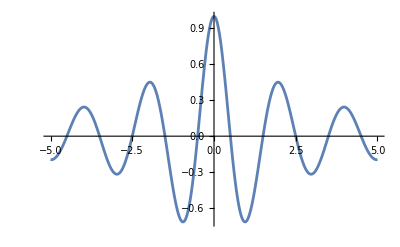

b)

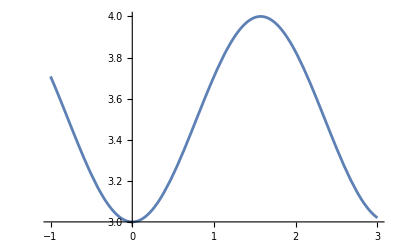

c)

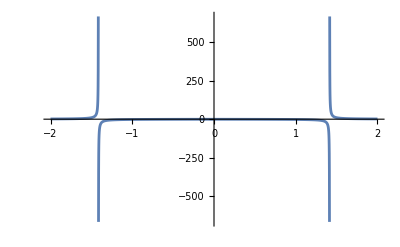

d)

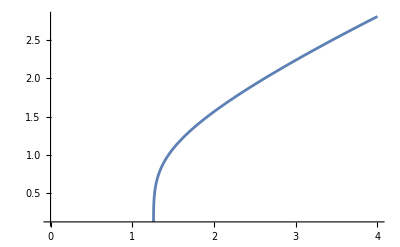

Since the domain of the function is [2^(1/3), Infinity) nothing is drawn from 0 to 2^(1/3)

```mathematica
"a)"
Plot[Cos[Pi x]/Sqrt[x^2+1],{x,-5,5}]
"b)"
Plot[Sin[x]^2+3, {x,-1,3}, PlotRange->Full]
"c)"
Plot[(Abs[x]+1)/(x^2-2), {x,-2,2}, PlotRange->Full]
"d)"
Plot[(x^3-2)^(1/4), {x,0,4}, PlotRange->Full]
Explanation= "Since the domain of the function is [2^(1/3), Infinity) nothing is drawn from 0 to 2^(1/3)"
```

#### Exercise Section.Equation

a) Make a graph of the function ArcTan[x]-ArcSin[x/(√(x^2+1))]on the interval [-4,4]. 
b) What do you see? Can you explain that?

#### Answer

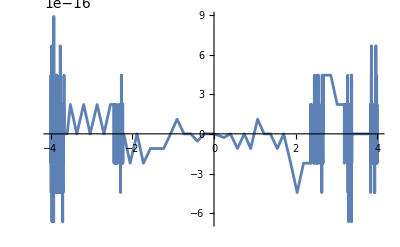

The graph is jagged and not smooth. The reason may be because the values are very small and the algorithm cannot be that precise.

```mathematica
Plot[ArcTan[x]-ArcSin[x/Sqrt[x^2+1]], {x,-4,4}]
Explanation="The graph is jagged and not smooth. The reason may be because the values are very small and the algorithm cannot be that precise."
```

#### Exercise Section.Equation

Use the help function to look up ParametricPlot, ParametricPlot3D, ContourPlot.
Make an image of the following expressions:
a) (x-1)^2+(y+2)^2==4
b) (x+1)^2+(2y+1)^2==1
c) {sin(t)-t cos(t),cos(t)+t sin(t)}, 0≤t≤2 π.
d) {t cos(t),t sin(t),t}, 0≤t≤4.
e) {sin(2 t),sin(3 t)}, -π≤t≤2 π.
f) {(cos(u)+3) cos(t),(cos(u)+3) sin(t),sin(u)}, 0≤t≤2 π, 0≤u≤2 π

#### Answer

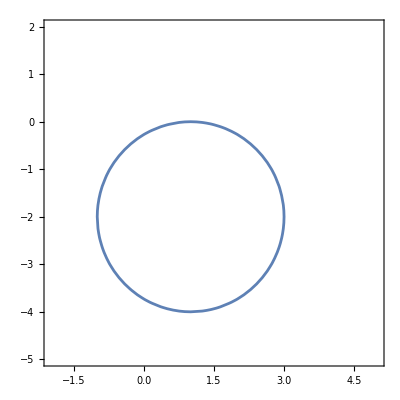

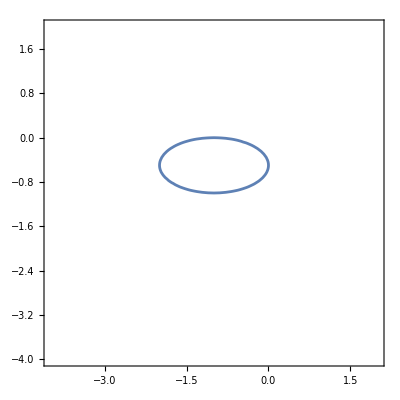

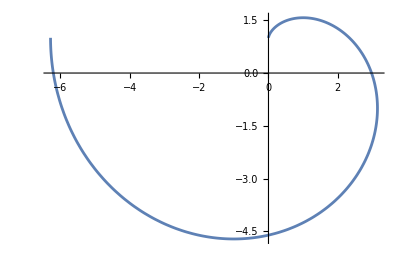

-Graphics3D-

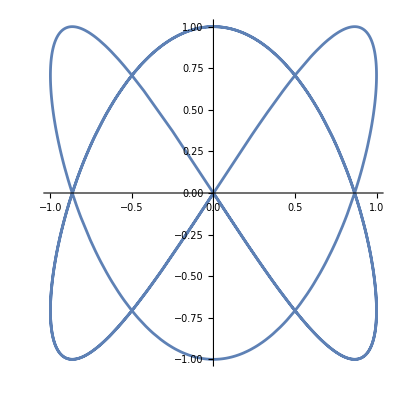

-Graphics3D-

```mathematica
ContourPlot[(x-1)^2+(y+2)^2 == 4,{x,-2, 5}, {y,-5,2}, AspectRatio->Automatic]

ContourPlot[(x+1)^2+(2y+1)^2==1, {x,-4,2}, {y,-4,2}, AspectRatio->Automatic]

ParametricPlot[{Sin[t]-t*Cos[t], Cos[t]+t*Sin[t]}, {t,0,2Pi}]

ParametricPlot3D[{t*Cos[t],t*Sin[t],t}, {t, 0, 4}]

ParametricPlot[{Sin[2t], Sin[3t]}, {t,-Pi, 2Pi}]

ParametricPlot3D[{(Cos[u]+3)Cos[t],(Cos[u]+3)Sin[t], Sin[u]}, {t,0,2Pi}, {u,0,2Pi}]
```